# Combine Plots

```mathematica
ClearAll["Global`*"]
```

## Prerequisites

Need to run following codes to generate the data files:

High-T expansion result: phase_transition/highT.nb to generate phase_transition/output/highT.m
Instability scale solution: model_setup/instability.nb to generate model_setup/output/instable_scale.csv

## Instability scale

```mathematica
scalelist=Import[NotebookDirectory[]<>"/model_setup/output/instable_scale.csv"];
instable‵scale[mS_,sinθ_]:=Interpolation[scalelist][mS,sinθ];
```

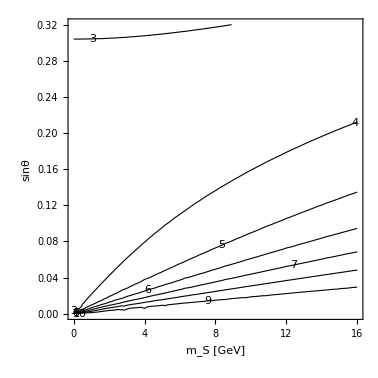

```mathematica
scale‵plot=ContourPlot[instable‵scale[mS,sinθ],{mS,0,16},{sinθ,0,0.32},ContourLabels->True,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

## High-T phase transition

```mathematica
DumpGet[NotebookDirectory[]<>"/phase_transition/output/highT.m"]
```

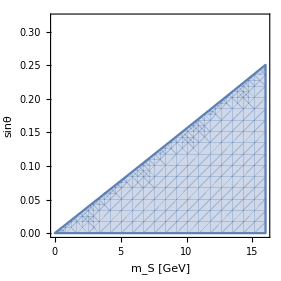

```mathematica
HighT‵SFOPT‵plot=RegionPlot[{strength[mS,sinθ]≤1.},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},BoundaryStyle->ColorData[97,"ColorList"][[1]]]
```

## LEP bound

```mathematica
boundlist=Import[NotebookDirectory[]<>"/collider/output/LEPbound.csv"];
boundfunc[mS_]:=Interpolation[boundlist][mS]
```

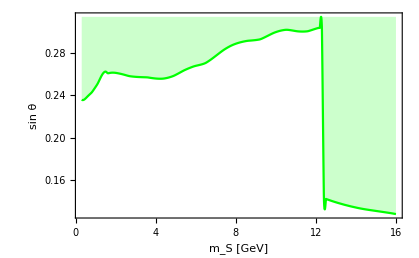

```mathematica
LEP‵plot=Plot[boundfunc[mS],{mS,0.3,16},Filling->Top,PlotStyle->Green,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sin θ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

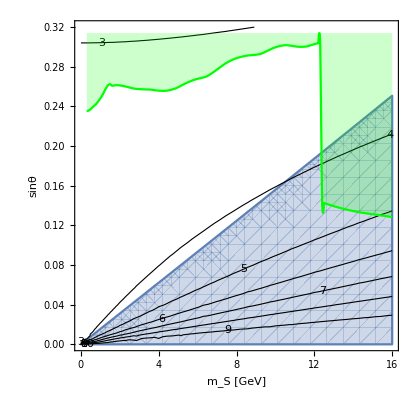

```mathematica
Show[HighT‵SFOPT‵plot,scale‵plot,LEP‵plot]
```